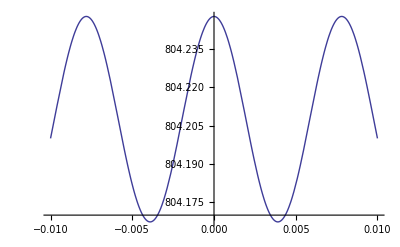

```mathematica
f[L_]:=FindRoot [Cos[x*L]-Cos[x]-20000*Sin[x]/(x),{x,804}]
Plot[x/.f[L], {L,-0.01, 0.01}]
```

```mathematica
Needs["PlotLegends`"]
```

PlotLegend::shdw: Symbol "PlotLegend" appears in multiple contexts {"PlotLegends`", "Global`"}; definitions in context "PlotLegends`" may shadow or be shadowed by other definitions.

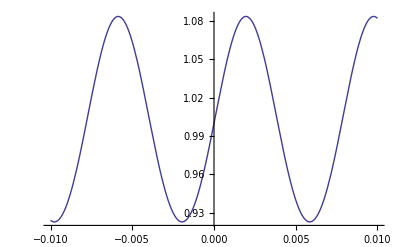

```mathematica
Plot[(Sin[(x/.f[L])*0.5*(1-L)])^2/(Sin[(x/.f[L])*0.5*(1+L)])^2,{L,-0.01, 0.01}]
```

```mathematica
JurassicPark=ToRules[p2==0.00000001 && p1 ==0.001 && p3 ==0.001 && A==10000 && z==256*3.141592653585]
```

{p2→1.×10^-8,p1→0.001,p3→0.001,A→10000,z→804.248}

Plot::nonopt: Options expected (instead of t6[L]) beyond position 2 in Plot[x/. f[L], {L, -0.01, 0.01}, t6[L]]
. An option must be a rule or a list of rules.

Plot[x/.f[L],{L,-0.01,0.01},t6[L]]

```mathematica
t2[L_]:=(8 ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)))/(ⅇ^(-2 ⅈ (x/.f[L]) L) (x/.f[L])^2*A*A (2-ⅈ (x/.f[L])*A p1) p2 p3+ⅇ^(2 ⅈ (x/.f[L]) 0.5*(1-L)) (x/.f[L])^2*A*A p1 (2+ⅈ (x/.f[L])*A p2) p3+(x/.f[L])^2*A*A p1 p2 (2-ⅈ (x/.f[L])*A p3)+ⅈ ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) (2 ⅈ+(x/.f[L])*A p1) (2 ⅈ+(x/.f[L])*A p2) (2 ⅈ+(x/.f[L])*A p3)) /. JurassicPark
```

```mathematica
(*This is the transmission for the case when we are pumping from one side...this is g*)
```

```mathematica
t6[L_]:= z*(p2*A*0.5*(Cos[z*L]-1)) /.JurassicPark     (* This it the analytic wave number difference..wave number shift*)
```

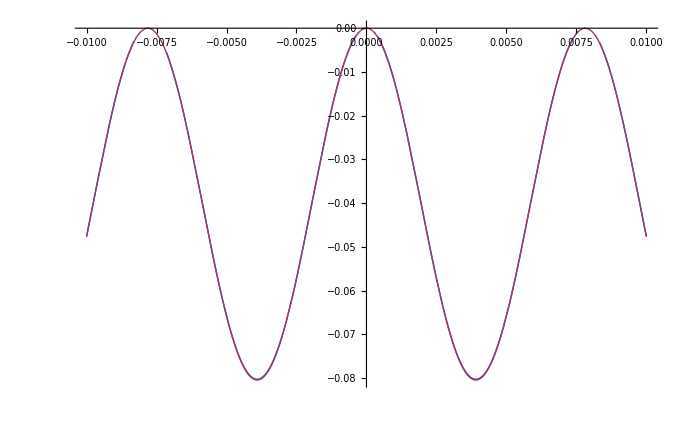

```mathematica
Plot[{ArcTan[(t2[L]-(Conjugate[t2[L]]) )/(2 ⅈ), 0.5*(t2[L]+(Conjugate[t2[L]]) )],t6[L]},{L,-0.01,0.01}]
```

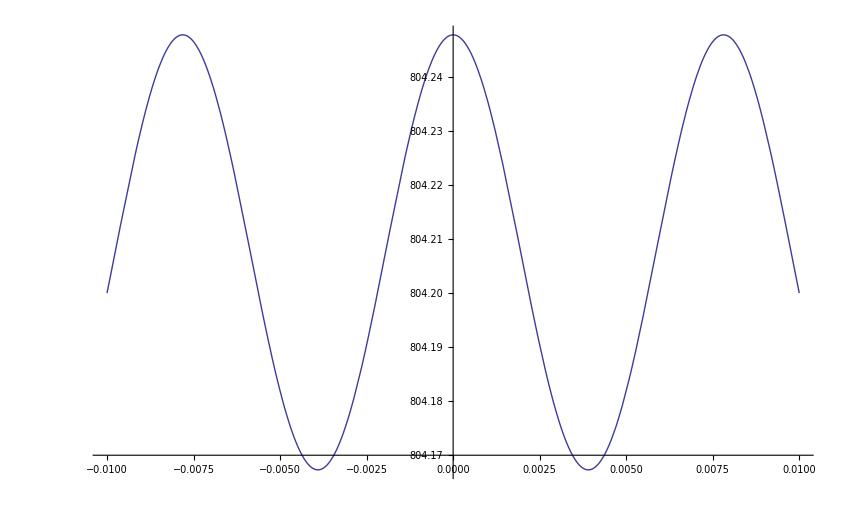

```mathematica
Plot[{t6[L]+256*3.141592653585,},{L,-0.01,0.01}]
```

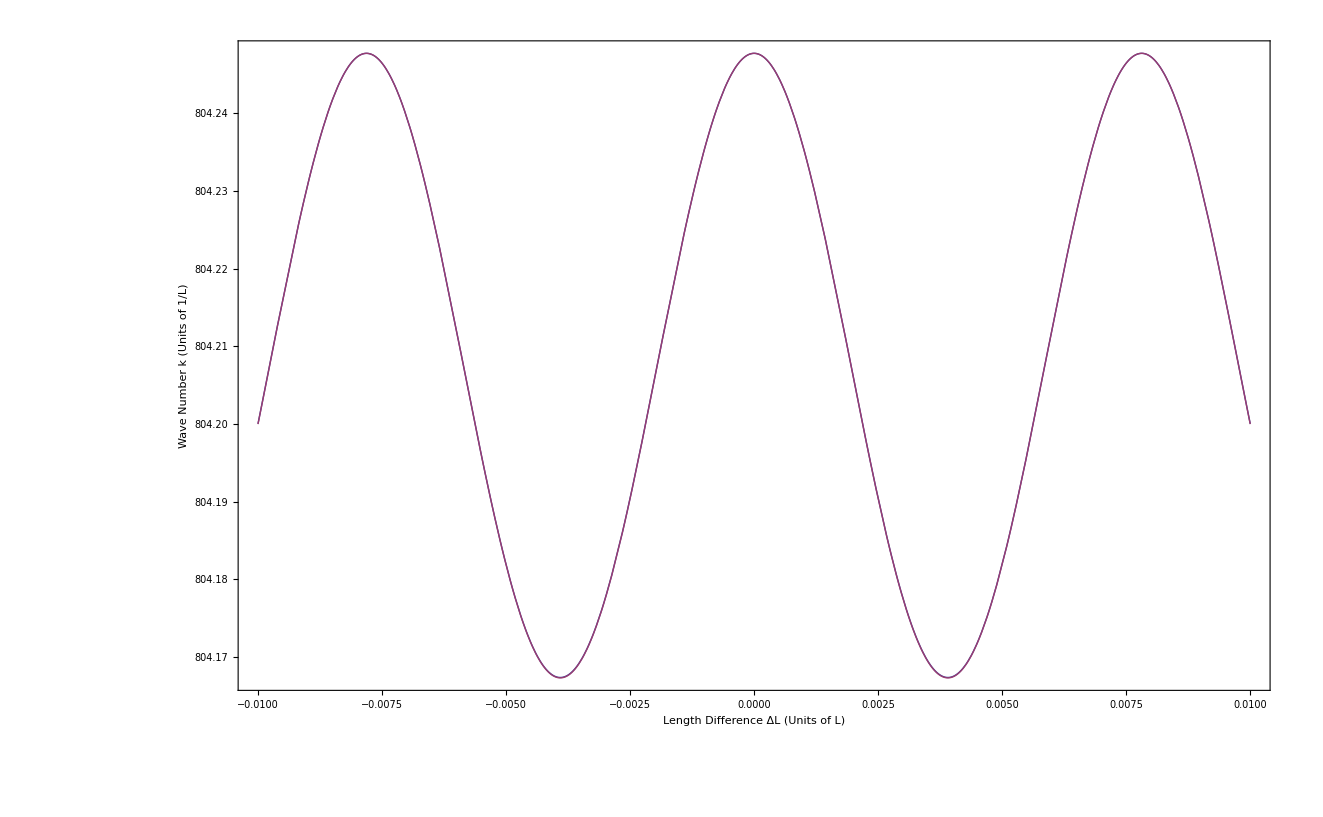

Plot::optx: Unknown option PlotLegends in Plot[{x/. f[L], t6[L] + 256\ 3.14159}, {L, -0.01, 0.01}, Frame → True, LabelStyle → Directive[FontFamily → "Times", FontSize → 16], FrameLabel → {"Length Difference \[CapitalDelta]L (Units of L)", "Wave Number k (Units of 1/L)"}, PlotLegends → {"Analytic", "Numeric"}]
.

Plot[{x/.f[L],t6[L]+256 3.14159},{L,-0.01,0.01},Frame→True,LabelStyle→Directive[FontFamily→Times,FontSize→16],FrameLabel→{Length Difference ΔL (Units of L),Wave Number k (Units of 1/L)},PlotLegends→{Analytic,Numeric}]

```mathematica
Plot[{x/.f[L],t6[L]+256*3.141592653585},{L,-0.01,0.01},Frame->True,LabelStyle->Directive[FontFamily->"Times",FontSize->16],FrameLabel->{"Length Difference ΔL (Units of L)","Wave Number k (Units of 1/L)"}]
```

```mathematica
t3[L_,x_]:=(8 ⅇ^(-2 ⅈ x 0.5*(1+L)))/(ⅇ^(-2 ⅈ x L) x^2*A*A (2-ⅈ x*A p1) p2 p3+ⅇ^(2 ⅈ x 0.5*(1-L)) x^2*A*A p1 (2+ⅈ x*A p2) p3+x^2*A*A p1 p2 (2-ⅈ x*A p3)+ⅈ ⅇ^(-2 ⅈ x 0.5*(1+L)) (2 ⅈ+x*A p1) (2 ⅈ+x*A p2) (2 ⅈ+x*A p3)) /.JurassicPark
(*Here I'm interested in what happens when the wave number x or z respectively, don't change with the mirror position.  In the graph above, for each central mirror position, the wave number is recalculated and plotted.  This is like always pumping at the entire atom-cavity resonance*)
```

```mathematica
t5[L_]:=(8 ⅇ^(-2 ⅈ z 0.5*(1+L)))/(ⅇ^(-2 ⅈ z L) z^2*A*A (2-ⅈ z*A p1) p2 p3+ⅇ^(2 ⅈ z 0.5*(1-L)) z^2*A*A p1 (2+ⅈ z*A p2) p3+z^2*A*A p1 p2 (2-ⅈ z*A p3)+ⅈ ⅇ^(-2 ⅈ z 0.5*(1+L)) (2 ⅈ+z*A p1) (2 ⅈ+z*A p2) (2 ⅈ+z*A p3)) /.JurassicPark
```

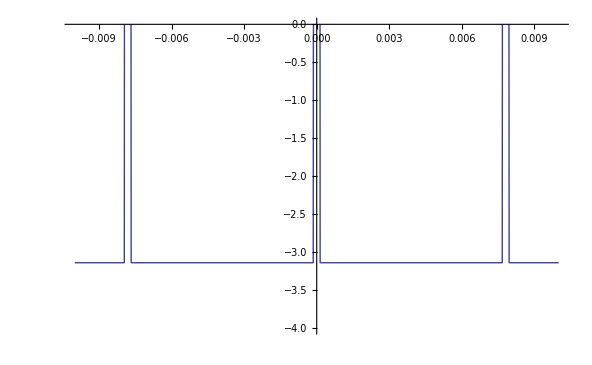

```mathematica
Plot[{ArcTan[(t5[L]-(Conjugate[t5[L]]) )/(2 ⅈ), 0.5*(t5[L]+(Conjugate[t5[L]]) )]},{L,-0.01,0.01},PlotRange->{-4,0}]
```

```mathematica
Plot3D[ArcTan[(t3[L,x]-(Conjugate[t3[L,x]]) )/(2 ⅈ), 0.5*(t3[L,x]+(Conjugate[t3[L,x]]) )], {L,-0.01,0.01},{x,795,805},PlotRange->{1,5}]
```

-Graphics3D-

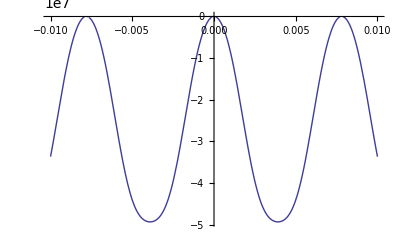

```mathematica
Plot[{(ArcTan[(t2[L]-(Conjugate[t2[L]]) )/(2 ⅈ), 0.5*(t2[L]+(Conjugate[t2[L]]) )])/(t2[L]*(Conjugate[t2[L]]))},{L,-0.01,0.01}]
```

```mathematica
t7[L_,r_]:=(8 ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)))/(ⅇ^(-2 ⅈ (x/.f[L]) L) (x/.f[L])^2*A*A (2-ⅈ (x/.f[L])*A r) p2 r+ⅇ^(2 ⅈ (x/.f[L]) 0.5*(1-L)) (x/.f[L])^2*A*A r (2+ⅈ (x/.f[L])*A p2) r+(x/.f[L])^2*A*A r p2 (2-ⅈ (x/.f[L])*A r)+ⅈ ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) (2 ⅈ+(x/.f[L])*A r) (2 ⅈ+(x/.f[L])*A p2) (2 ⅈ+(x/.f[L])*A r)) /. JurassicPark
```

```mathematica
Plot3D[ArcTan[(t7[L,r]-(Conjugate[t7[L,r]]) )/(2 ⅈ), 0.5*(t7[L,r]+(Conjugate[t7[L,r]]) )], {L,-0.01,0.01},{r,0,0.000001}]
```

-Graphics3D-

```mathematica
t8[L_]:= (-1/(p2*z*A)-0.5*Sin[z*L])/(-1/(p2*z*A)+0.5*Sin[z*L]) /. JurassicPark
```

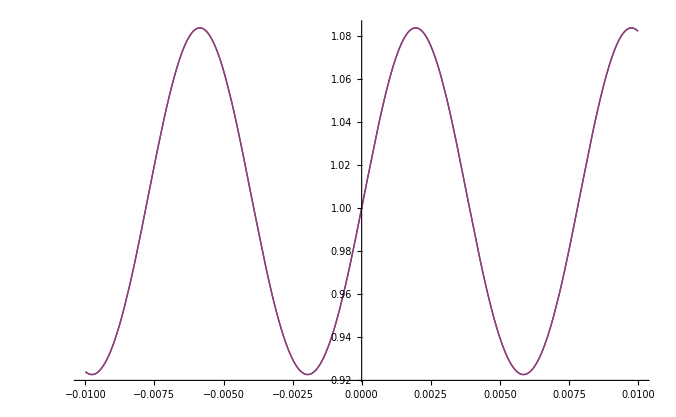

```mathematica
Plot[{(Sin[(x/.f[L])*0.5*(1-L)])^2/(Sin[(x/.f[L])*0.5*(1+L)])^2,t8[L]},{L,-0.01, 0.01}]
```

```mathematica
(*Here I've plotted the approximation for A/B squared vs. the approximation I've done in the lyx file*)
```

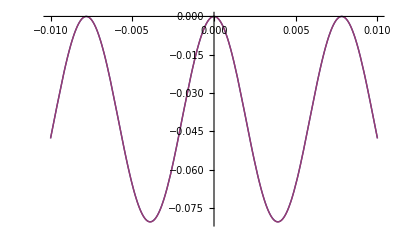

```mathematica
Plot[{(x/.f[L])-804.24771931776,t6[L]},{L,-0.01,0.01}]
```

```mathematica
(*This is a plot of the analytic wavenumber shift vs the numeric shift.  I did this because I realized the first calculation of the phase of the outgoing wave in the slightly transmissive case was always just going to be the same value as it is going to be whatever I am pumping it with. *)
```

```mathematica
(*Now I'd like to look at the Asboth force broken up into the coherent reflected part and the incoherent refelected part.  I want to see if including only one of them will lead to Abraham while including both will lead to Minkowski*)
```

```mathematica
y1[L_]:= 0.25*((Sin[(x/.f[L])*0.5*(1-L)])^2/(Sin[(x/.f[L])*0.5*(1+L)])^2 -1) (*This is the total Asboth force taking B=1 and /epsilon_0 = 1*)
```

```mathematica
y2[L_] := (x/.f[L])*(x/.f[L])*A*A*p2*p2*0.25*0.25*((Sin[(x/.f[L])*0.5*(1-L)])^2/(Sin[(x/.f[L])*0.5*(1+L)])^2 -1)  /. JurassicPark(*reflection force*)
```

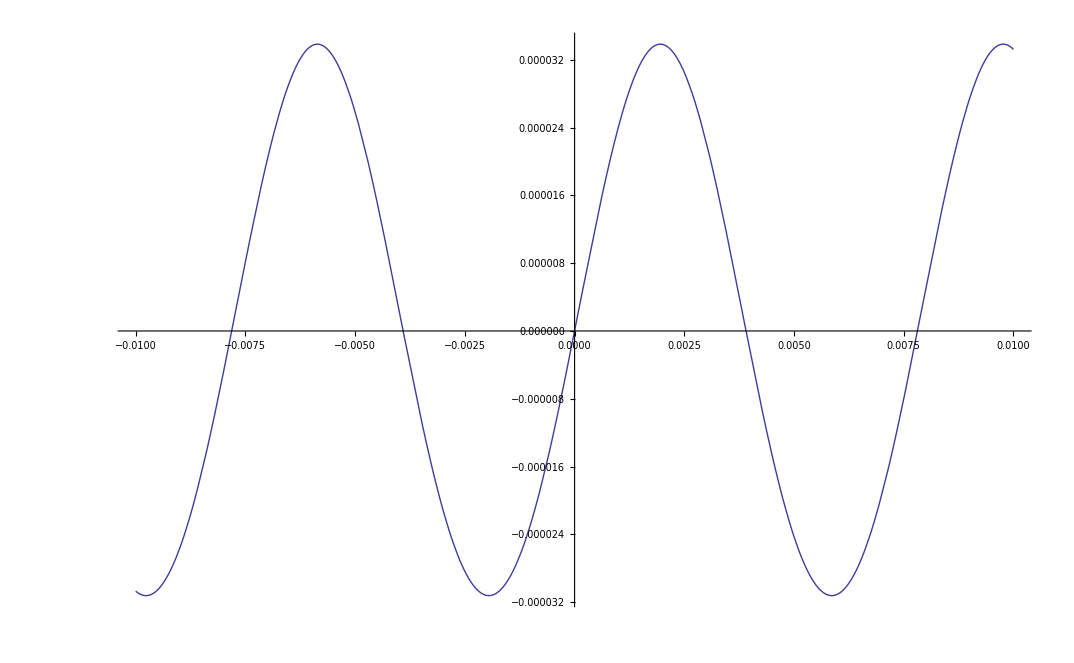

```mathematica
Plot[y2[L],{L,-0.01, 0.01}] (*incoherent reflection component*)
```

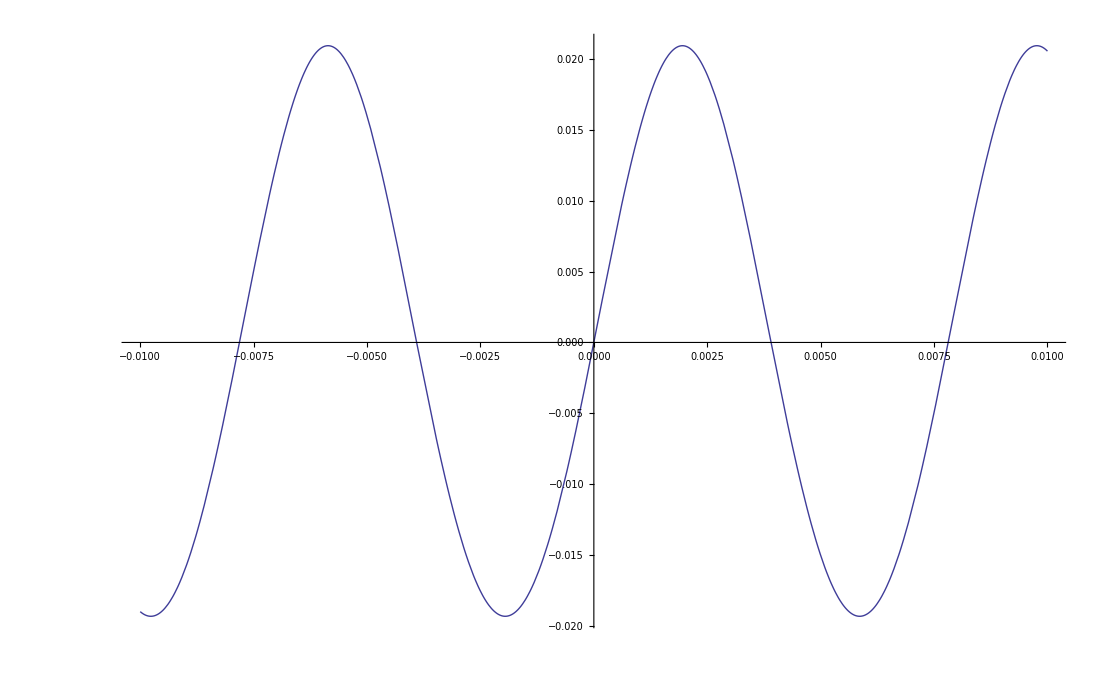

```mathematica
Plot[y1[L],{L,-0.01, 0.01}] (*This is the total Asboth force (not including poynting component) I'm taking B=1, epsilon_0=1*)
```

```mathematica
y3[L_]:= -0.25*(x/.f[L])*A*p2*(Sin[(x/.f[L])*0.5*(1-L)])/(Sin[(x/.f[L])*0.5*(1+L)])*Sin[(x/.f[L])*L] /.JurassicPark (*Coherent reflection part*)
```

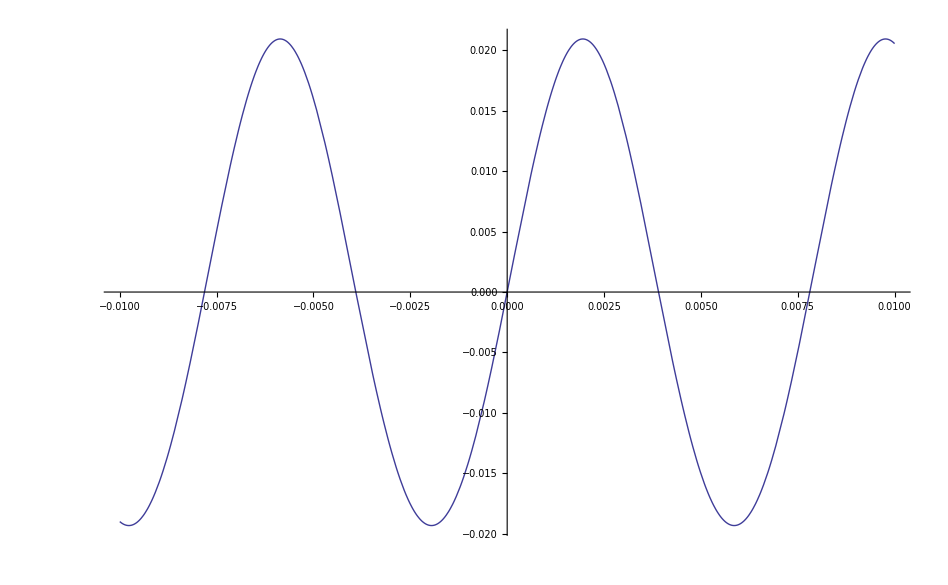

```mathematica
Plot[y3[L],{L,-0.01, 0.01}]
```

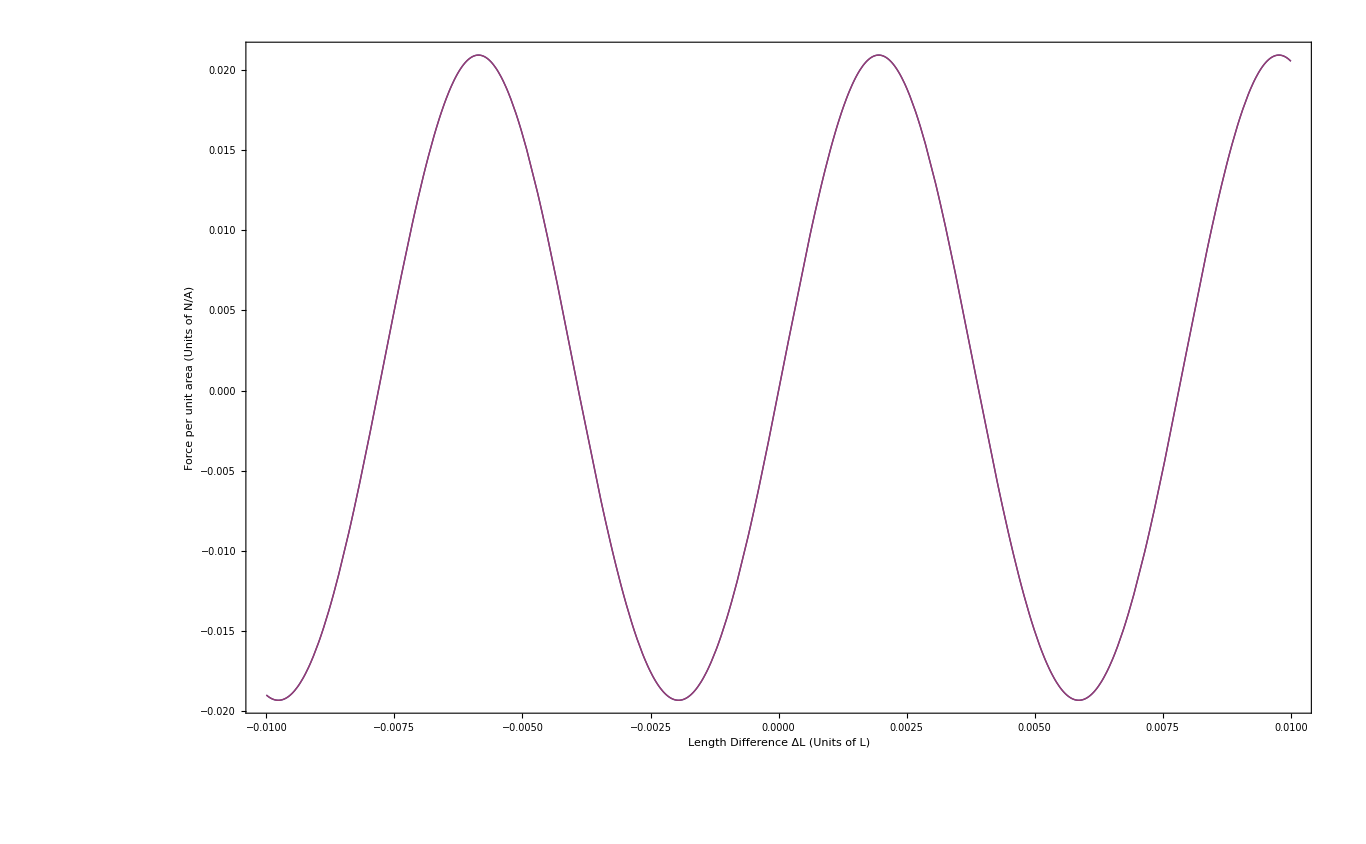

```mathematica
Plot[{y3[L],y1[L]},{L,-0.01, 0.01},Frame->True,LabelStyle->Directive[FontFamily->"Times",FontSize->16],FrameLabel->{"Length Difference ΔL (Units of L)","Force per unit area  (Units of N/A)"}]
```